## CA Manipulation

```mathematica
initialValues=SparseArray[{{1,1}->1,{2,5}->1,{3,10}->1,{1,6}->1},{5,11}]; (* Define starting values and lattice size. *)
```

```mathematica
cellState[cell_,globalState_]:=globalState[[cell[[1]],cell[[2]]]]; (* Returns the value of the cell {x,y}. *)
```

```mathematica
triangularvNN[cell_,lattice_]:=Module[{c1=cell[[1]],c2=cell[[2]]},
If[EvenQ[c2],
{c1,c2}->{{c1,c2-1},{c1,c2},{c1,c2+1},{c1+1,c2-1}},
{c1,c2}->{{c1-1,c2+1},{c1,c2-1},{c1,c2},{c1,c2+1}}
]
]; (* Associates the cell to its triangular von Neumann Neighborhood. *)
```

```mathematica
nbhdTable[lattice_]:=Association[Flatten[Table[triangularvNN[{i,j},lattice],{i,1,Dimensions[lattice][[1]]},{j,1,Dimensions[lattice][[2]]}],1]]; (* Associates all cells to their triangular von Neumann neighborhoods. *)
```

```mathematica
vonNeumannNeighborhoods=nbhdTable[initialValues]; (* Evaluate once and use henceforth! *)
```

```mathematica
neighborhoodState[cell_,globalState_]:=Quiet[Module[{n=vonNeumannNeighborhoods[[Key[cell]]]},
Table[If[IntegerQ[cellState[n[[i]],globalState]],cellState[n[[i]],globalState],0],
{i,1,Length[n]}]
]]; (* Returns the state of each cell in the von Neumann neighborhood of the specified cell. *)
```

```mathematica
rules=<|{0,0}->0,{0,1}->1,{0,2}->1,{0,3}->1,{1,1}->0,{1,2}->0,{1,3}->1,{1,4}->1|>; (* An example set of rules. *)
```

```mathematica
cellEvolution[cell_,globalState_,rules_]:=Lookup[rules,{{cellState[cell,globalState],Total[neighborhoodState[cell,globalState]]}}][[1]];(* Applies the specified evolution rule to the particular cell. *)
```

```mathematica
globalEvolution[state_,rules_]:=SparseArray[{i_,j_}:>cellEvolution[{i,j},state,rules],Dimensions[state]]; (* Applies the specified rule to the current state. *)
```

## CA Graphics

#### 2D Graphics

11

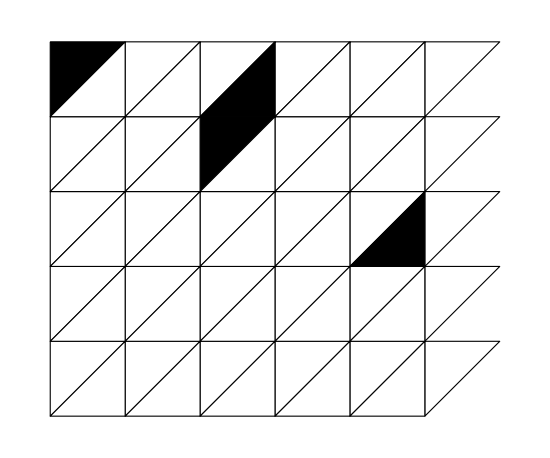

```mathematica
tLatticePlot[lattice_,basis_:{{1,0},{0,1}}]:=Graphics[Module[{b1=basis[[1]],b2={-basis[[2,1]],basis[[2,2]]},d1=Dimensions[lattice][[1]],d2=Dimensions[lattice][[2]]},
Table[
If[OddQ[j],
{FaceForm[GrayLevel[1-cellState[{i,j},lattice]]],EdgeForm[Black],Triangle[{b1*((j-1)/2)-b2*(i-1),b1*((j+1)/2)-b2*(i-1),b1*(j-1)/2-b2*(i)}]},
{FaceForm[GrayLevel[1-cellState[{i,j},lattice]]],EdgeForm[Black],Triangle[{b1*(j/2)-b2*(i-1),b1*(j/2-1)-b2*(i),b1*(j/2)-b2*(i)}]}],
{i,1,d1},{j,1,d2}]],ImageSize->50*Dimensions[lattice][[2]]
]; (* Plots the triangular lattice with given state. *)
Dimensions[initialValues][[2]]
tLatticePlot[initialValues]
```

#### 1D Graphics

11

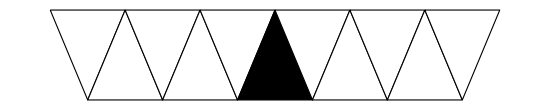

```mathematica
initialValues1D=SparseArray[{{1,6}->1},{1,11}];
basis1D={{1,0},{0.5,Sqrt[3]/2}};
Dimensions[initialValues1D][[2]]
tLatticePlot[initialValues1D,basis1D]
```

```mathematica
T=10;
Manipulate[
With[{c=NestList[globalEvolution[#,rules]&,initialValues1D,T]},
Graphics[tLatticePlot[c[[n]],basis1D]]
],{{n,1},1,T+1,1},SaveDefinitions->True
]
```